# Chaotic systems

## The Lorenz attractor

Fixed points

{{-8.52291,-8.52291,27.24},{0.,0.,0.},{8.52291,8.52291,27.24}}

-Graphics3D-

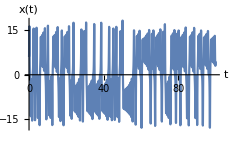
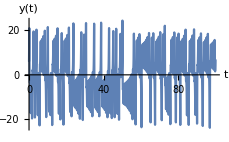
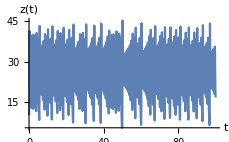

```mathematica
tmax=100;x0=6.1;y0=6;z0=10;
d=10;
r=28.24;
b=8/3;

diffx=d (y-x);
diffy=r x-y-x z;
diffz=x y-b z;

soln=NDSolve[{
x'[t]==Evaluate[diffx/.{x->x[t],y->y[t],z->z[t]}],
y'[t]==Evaluate[diffy/.{x->x[t],y->y[t],z->z[t]}],
z'[t]==Evaluate[diffz/.{x->x[t],y->y[t],z->z[t]}],
x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,tmax},MaxSteps->Infinity];
fixedpoints=Quiet[Solve[{diffx==0,diffy==0,diffz==0},{x,y,z}]];
Print[Style["Fixed points",18,Blue]]
coordinates={x,y,z}/.fixedpoints
Gfp=Graphics3D[{PointSize[0.03],Red,Point[coordinates]}];
pplot=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.soln],{t,0,tmax},PlotPoints->1000,AxesLabel->{x[t],y[t],z[t]},PlotStyle->Thin,LabelStyle->18];
Show[pplot,Gfp]
px=Plot[Evaluate[x[t]/.soln],{t,0,tmax},AxesLabel-> {t,x[t]},PlotRange-> All,ImageSize->230,LabelStyle->18];
py=Plot[Evaluate[y[t]/.soln],{t,0,tmax},AxesLabel-> {t,y[t]},PlotRange-> All,ImageSize->230,LabelStyle->18];
pz=Plot[Evaluate[z[t]/.soln],{t,0,tmax},AxesLabel-> {t,z[t]},PlotRange-> All,ImageSize->230,LabelStyle->18];
Row[{px,py,pz}]
```

## The Rössler attractor

Fixed points

{{0.0052546,-0.0250219,0.0250219},{5.99475,-28.5464,28.5464}}

-Graphics3D-

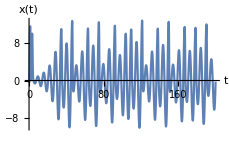
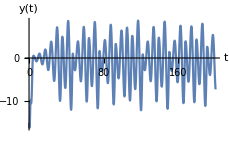
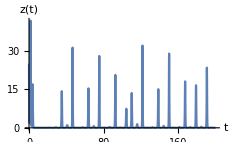

```mathematica
tmax=200;x0=0;y0=-15;z0=25;
a=0.21;
b=0.15;
c=6;

diffx=-(y+z);
diffy=x+a y;
diffz=b+x z-c z;

soln=NDSolve[{
x'[t]==Evaluate[diffx/.{x->x[t],y->y[t],z->z[t]}],
y'[t]==Evaluate[diffy/.{x->x[t],y->y[t],z->z[t]}],
z'[t]==Evaluate[diffz/.{x->x[t],y->y[t],z->z[t]}],
x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,tmax},MaxSteps->Infinity];
fixedpoints=Quiet[Solve[{diffx==0,diffy==0,diffz==0},{x,y,z}]];
Print[Style["Fixed points",18,Blue]]
coordinates={x,y,z}/.fixedpoints
Gfp=Graphics3D[{PointSize[0.03],Red,Point[coordinates]}];
pplot=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.soln],{t,0,tmax},PlotPoints->1000,AxesLabel->{x[t],y[t],z[t]},PlotStyle->Thin,BoxRatios->{1,1,1},PlotRange->All,LabelStyle->18];
Show[pplot,Gfp]
Row[{Plot[Evaluate[x[t]/.soln],{t,0,tmax},AxesLabel-> {t,x[t]},PlotRange-> All,ImageSize->230,LabelStyle->18],
Plot[Evaluate[y[t]/.soln],{t,0,tmax},AxesLabel-> {t,y[t]},PlotRange-> All,ImageSize->230,LabelStyle->18],
Plot[Evaluate[z[t]/.soln],{t,0,tmax},AxesLabel-> {t,z[t]},PlotRange-> All,ImageSize->230,LabelStyle->18]}]
```

## Rössler attractor with two initial conditions (demonstration of chaos)

Fixed points

{{0.0052546,-0.0250219,0.0250219},{5.99475,-28.5464,28.5464}}

-Graphics3D-

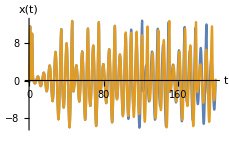
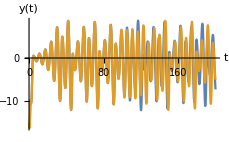
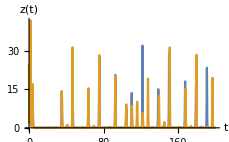

```mathematica
tmax=200;x0=0;y0=-15;z0=25;dx0=0.0;dy0=0;dz0=0.004;
a=0.21;
b=0.15;
c=6;

diffx=-(y+z);
diffy=x+a y;
diffz=b+x z-c z;

sol1=NDSolve[{x'[t]==Evaluate[diffx/.{x->x[t],y->y[t],z->z[t]}],
y'[t]==Evaluate[diffy/.{x->x[t],y->y[t],z->z[t]}],
z'[t]==Evaluate[diffz/.{x->x[t],y->y[t],z->z[t]}],
x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,tmax}];
sol2=NDSolve[{x'[t]==Evaluate[diffx/.{x->x[t],y->y[t],z->z[t]}],
y'[t]==Evaluate[diffy/.{x->x[t],y->y[t],z->z[t]}],
z'[t]==Evaluate[diffz/.{x->x[t],y->y[t],z->z[t]}],
x[0]==x0+dx0,y[0]==y0+dy0,z[0]==z0+dz0},{x,y,z},{t,0,tmax}];
fixedpoints=Quiet[Solve[{diffx==0,diffy==0,diffz==0},{x,y,z}]];
Print[Style["Fixed points",18,Blue]]
coordinates={x,y,z}/.fixedpoints
Gfp=Graphics3D[{PointSize[0.03],Red,Point[coordinates]}];
p1=ParametricPlot3D[{Evaluate[{x[t],y[t],z[t]}/.sol1],Evaluate[{x[t],y[t],z[t]}/.sol2]},
{t,0,tmax},PlotPoints->2000,AxesLabel->{x[t],y[t],z[t]},PlotStyle->Thin,BoxRatios->{1,1,1},PlotRange->All,LabelStyle->18];
Show[p1,Gfp]
Row[{Plot[{Evaluate[x[t]/.sol1],Evaluate[x[t]/.sol2]},{t,0,tmax},AxesLabel-> {t,x[t]},PlotRange-> All,ImageSize->230,LabelStyle->18],
Plot[{Evaluate[y[t]/.sol1],Evaluate[y[t]/.sol2]},{t,0,tmax},AxesLabel-> {t,y[t]},PlotRange-> All,ImageSize->230,LabelStyle->18],
Plot[{Evaluate[z[t]/.sol1],Evaluate[z[t]/.sol2]},{t,0,tmax},AxesLabel-> {t,z[t]},PlotRange-> All,ImageSize->230,LabelStyle->18]}]
```

## The Chen attractor

Fixed points

{{0,0,0},{-3 √7,-3 √7,21},{3 √7,3 √7,21}}

-Graphics3D-

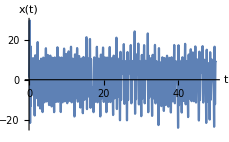
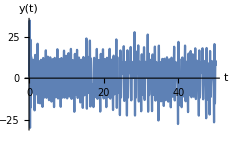
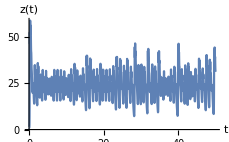

```mathematica
tmax=50;x0=1;y0=1;z0=1;
a=35;
b=3;
c=28;

diffx=a (y-x);
diffy=(c-a) x-x z+c y;
diffz=x y-b z;

soln=NDSolve[{
x'[t]==Evaluate[diffx/.{x->x[t],y->y[t],z->z[t]}],
y'[t]==Evaluate[diffy/.{x->x[t],y->y[t],z->z[t]}],
z'[t]==Evaluate[diffz/.{x->x[t],y->y[t],z->z[t]}],
x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,tmax},MaxSteps->Infinity];
fixedpoints=Solve[{diffx==0,diffy==0,diffz==0},{x,y,z}];
Print[Style["Fixed points",18,Blue]]
coordinates={x,y,z}/.fixedpoints
Gfp=Graphics3D[{PointSize[0.03],Red,Point[coordinates]}];
pplot=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.soln],{t,0,tmax},PlotPoints->1000,AxesLabel->{x[t],y[t],z[t]},PlotStyle->Thin,BoxRatios->{1,1,1},PlotRange->All,LabelStyle->18];
Show[pplot,Gfp]
Row[{Plot[Evaluate[x[t]/.soln],{t,0,tmax},AxesLabel-> {t,x[t]},PlotRange-> All,ImageSize->230,LabelStyle->18],
Plot[Evaluate[y[t]/.soln],{t,0,tmax},AxesLabel-> {t,y[t]},PlotRange-> All,ImageSize->230,LabelStyle->18],
Plot[Evaluate[z[t]/.soln],{t,0,tmax},AxesLabel-> {t,z[t]},PlotRange-> All,ImageSize->230,LabelStyle->18]}]
```

## The modified Chen attractor

Fixed points

{{-7.31628+0. ⅈ,-7.31628+0. ⅈ,17.8427+0. ⅈ},{-1.12245+0. ⅈ,-1.12245+0. ⅈ,0.419962+0. ⅈ},{8.43873+0. ⅈ,8.43873+0. ⅈ,23.7374+0. ⅈ}}

-Graphics3D-

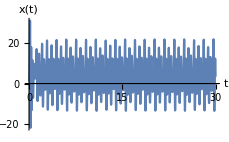
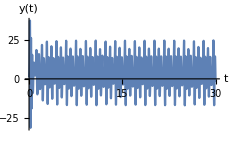
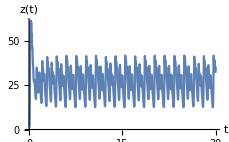

```mathematica
tmax=30;x0=1;y0=1;z0=1;
a=35;
b=3;
c=28;
m=23.1;

diffx=a (y-x);
diffy=(c-a) x-x z+c y+m;
diffz=x y-b z;

soln=NDSolve[{
x'[t]==Evaluate[diffx/.{x->x[t],y->y[t],z->z[t]}],
y'[t]==Evaluate[diffy/.{x->x[t],y->y[t],z->z[t]}],
z'[t]==Evaluate[diffz/.{x->x[t],y->y[t],z->z[t]}],
x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,tmax},MaxSteps->Infinity];
fixedpoints=Quiet[Solve[{diffx==0,diffy==0,diffz==0},{x,y,z}]];
Print[Style["Fixed points",18,Blue]]
coordinates={x,y,z}/.fixedpoints
Gfp=Graphics3D[{PointSize[0.03],Red,Point[coordinates]}];
pplot=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.soln],{t,0,tmax},PlotPoints->1000,AxesLabel->{x[t],y[t],z[t]},PlotStyle->Thin,BoxRatios->{1,1,1},PlotRange->All,LabelStyle->18];
Show[pplot,Gfp]
Row[{Plot[Evaluate[x[t]/.soln],{t,0,tmax},AxesLabel-> {t,x[t]},PlotRange-> All,ImageSize->230,LabelStyle->18],
Plot[Evaluate[y[t]/.soln],{t,0,tmax},AxesLabel-> {t,y[t]},PlotRange-> All,ImageSize->230,LabelStyle->18],
Plot[Evaluate[z[t]/.soln],{t,0,tmax},AxesLabel-> {t,z[t]},PlotRange-> All,ImageSize->230,LabelStyle->18]}]
```

## The Lu attractor

Fixed points

{{0,0,0},{-5 √3,-5 √3,25},{5 √3,5 √3,25}}

-Graphics3D-

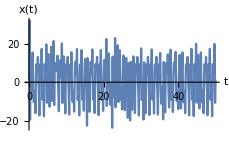
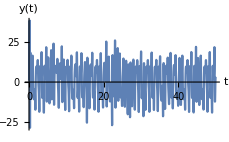
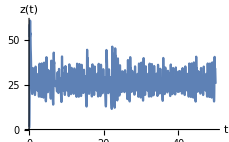

```mathematica
tmax=50;x0=1;y0=1;z0=1;
a=36;
b=3;
c=25;

diffx=a (y-x);
diffy=-x z+c y;
diffz=x y-b z;

soln=NDSolve[{
x'[t]==Evaluate[diffx/.{x->x[t],y->y[t],z->z[t]}],
y'[t]==Evaluate[diffy/.{x->x[t],y->y[t],z->z[t]}],
z'[t]==Evaluate[diffz/.{x->x[t],y->y[t],z->z[t]}],
x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,tmax},MaxSteps->Infinity];
fixedpoints=Solve[{diffx==0,diffy==0,diffz==0},{x,y,z}];
Print[Style["Fixed points",18,Blue]]
coordinates={x,y,z}/.fixedpoints
Gfp=Graphics3D[{PointSize[0.03],Red,Point[coordinates]}];
pplot=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.soln],{t,0,tmax},PlotPoints->1000,AxesLabel->{x[t],y[t],z[t]},PlotStyle->Thin,BoxRatios->{1,1,1},PlotRange->All,LabelStyle->18];
Show[pplot,Gfp]
Row[{Plot[Evaluate[x[t]/.soln],{t,0,tmax},AxesLabel-> {t,x[t]},PlotRange-> All,ImageSize->230,LabelStyle->18],
Plot[Evaluate[y[t]/.soln],{t,0,tmax},AxesLabel-> {t,y[t]},PlotRange-> All,ImageSize->230,LabelStyle->18],
Plot[Evaluate[z[t]/.soln],{t,0,tmax},AxesLabel-> {t,z[t]},PlotRange-> All,ImageSize->230,LabelStyle->18]}]
```

## The Pan-Xu-Zhou attractor

Fixed points

{{0,0,0},{-8 √(2/3),-8 √(2/3),16},{8 √(2/3),8 √(2/3),16}}

-Graphics3D-

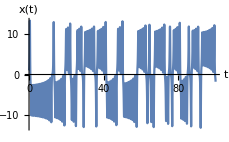
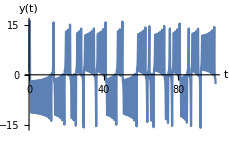
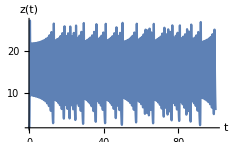

```mathematica
tmax=100;x0=1;y0=1;z0=2;
a=10;
b=8/3;
c=16;

diffx=a (y-x);
diffy=c x-x z;
diffz=x y-b z;

soln=NDSolve[{
x'[t]==Evaluate[diffx/.{x->x[t],y->y[t],z->z[t]}],
y'[t]==Evaluate[diffy/.{x->x[t],y->y[t],z->z[t]}],
z'[t]==Evaluate[diffz/.{x->x[t],y->y[t],z->z[t]}],
x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,tmax},MaxSteps->Infinity];
fixedpoints=Solve[{diffx==0,diffy==0,diffz==0},{x,y,z}];
Print[Style["Fixed points",18,Blue]]
coordinates={x,y,z}/.fixedpoints
Gfp=Graphics3D[{PointSize[0.03],Red,Point[coordinates]}];
pplot=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.soln],{t,0,tmax},PlotPoints->1000,AxesLabel->{x[t],y[t],z[t]},PlotStyle->Thin,BoxRatios->{1,1,1},PlotRange->All,LabelStyle->18];
Show[pplot,Gfp]
Row[{Plot[Evaluate[x[t]/.soln],{t,0,tmax},AxesLabel-> {t,x[t]},PlotRange-> All,ImageSize->230,LabelStyle->18],
Plot[Evaluate[y[t]/.soln],{t,0,tmax},AxesLabel-> {t,y[t]},PlotRange-> All,ImageSize->230,LabelStyle->18],
Plot[Evaluate[z[t]/.soln],{t,0,tmax},AxesLabel-> {t,z[t]},PlotRange-> All,ImageSize->230,LabelStyle->18]}]
```

## The Bouali attractor, proposed by Safieddine Bouali

Fixed points

{{0.,0.,0.}}

-Graphics3D-

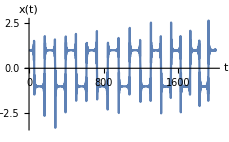
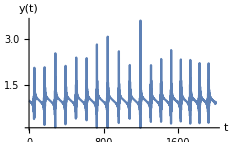
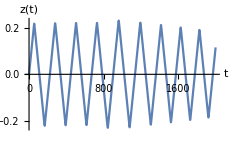

```mathematica
Clear[x,y,z,t,a,b,c,d]
tmax=2000;x0=1;y0=1;z0=0;

a=3;
b=2.2;
c=1.0;
d=0.004;

diffx=a x(1-y)-b z;
diffy=-c y(1-x^2);
diffz=d x;

soln=NDSolve[{
x'[t]==Evaluate[diffx/.{x->x[t],y->y[t],z->z[t]}],
y'[t]==Evaluate[diffy/.{x->x[t],y->y[t],z->z[t]}],
z'[t]==Evaluate[diffz/.{x->x[t],y->y[t],z->z[t]}],
x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,tmax},MaxSteps->Infinity];
fixedpoints=Quiet[Solve[{diffx==0,diffy==0,diffz==0},{x,y,z}]];
Print[Style["Fixed points",18,Blue]]
coordinates={x,y,z}/.fixedpoints
Gfp=Graphics3D[{PointSize[0.03],Red,Point[coordinates]}];
pplot=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.soln],{t,0,tmax},PlotPoints->1000,AxesLabel->{x[t],y[t],z[t]},PlotStyle->Thin,BoxRatios->{1,1,1},PlotRange->All,LabelStyle->18];
Show[pplot,Gfp]
Row[{Plot[Evaluate[x[t]/.soln],{t,0,tmax},AxesLabel-> {t,x[t]},PlotRange-> All,ImageSize->230,LabelStyle->18],
Plot[Evaluate[y[t]/.soln],{t,0,tmax},AxesLabel-> {t,y[t]},PlotRange-> All,ImageSize->230,LabelStyle->18],
Plot[Evaluate[z[t]/.soln],{t,0,tmax},AxesLabel-> {t,z[t]},PlotRange-> All,ImageSize->230,LabelStyle->18]}]
```

## The Sprott’s Algebraically Simplest Dissipative Chaotic Flow

Fixed points

{{0.,0.,0.}}

-Graphics3D-

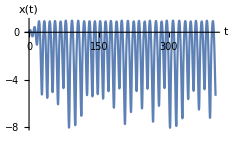
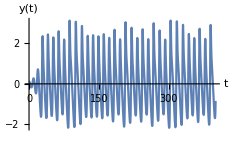
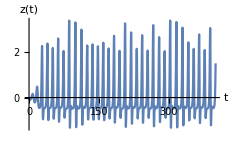

```mathematica
Clear[x,y,z,t,a]
tmax=400;x0=0.01;y0=0.1;z0=0.02;

a=2.017;

diffx=y;
diffy=z;
diffz=-a z-y^2-x;

soln=NDSolve[{
x'[t]==Evaluate[diffx/.{x->x[t],y->y[t],z->z[t]}],
y'[t]==Evaluate[diffy/.{x->x[t],y->y[t],z->z[t]}],
z'[t]==Evaluate[diffz/.{x->x[t],y->y[t],z->z[t]}],
x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,tmax},MaxSteps->Infinity];
fixedpoints=Quiet[Solve[{diffx==0,diffy==0,diffz==0},{x,y,z}]];
Print[Style["Fixed points",18,Blue]]
coordinates={x,y,z}/.fixedpoints
Gfp=Graphics3D[{PointSize[0.03],Red,Point[coordinates]}];
pplot=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.soln],{t,0,tmax},PlotPoints->1000,AxesLabel->{x[t],y[t],z[t]},PlotStyle->Thin,BoxRatios->{1,1,1},PlotRange->All,LabelStyle->18];
Show[pplot,Gfp]
Row[{Plot[Evaluate[x[t]/.soln],{t,0,tmax},AxesLabel-> {t,x[t]},PlotRange-> All,ImageSize->230,LabelStyle->18],
Plot[Evaluate[y[t]/.soln],{t,0,tmax},AxesLabel-> {t,y[t]},PlotRange-> All,ImageSize->230,LabelStyle->18],
Plot[Evaluate[z[t]/.soln],{t,0,tmax},AxesLabel-> {t,z[t]},PlotRange-> All,ImageSize->230,LabelStyle->18]}]
```

Creation of this notebook was supported by IT Academy program of Information Technology Foundation for Education (HITSA).